## Solution of differential equations

### Second-order DE

```mathematica
ode1={y''[x]+Sin[y[x]]==0,y[0]==2,y'[0]==1};
```

```mathematica
sol1=NDSolve[ode1,y,{x,-10,10}]
```

{{y→InterpolatingFunction[{{-10., 10.}}, <>]}}

```mathematica
Plot[y[x]/.sol,{x,-10,10}]
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

### Damped harmonic oscillator

```mathematica
osc[m_,b_,k_,x0_,v0_]:={x'[t]==v[t],v'[t]==-(b/m)*v[t]-(k/m)*x[t],x[0]==x0,v[0]==v0}
```

```mathematica
sol2=NDSolve[osc[10,10,500,1,0],{x,v},{t,0,6}]
```

{{x→InterpolatingFunction[{{0., 6.}}, <>],v→InterpolatingFunction[{{0., 6.}}, <>]}}

```mathematica
xsol[t_]:=x[t]/.sol2;vsol[t_]:=v[t]/.sol2;
```

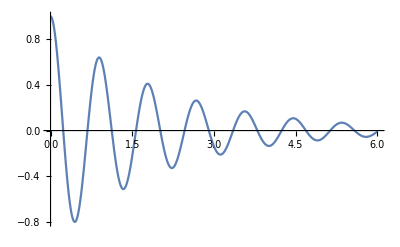

```mathematica
Plot[xsol[t],{t,0,6}]
```

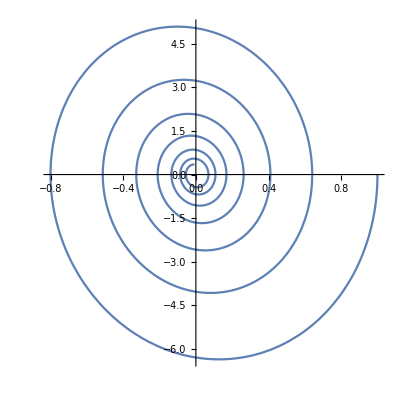

```mathematica
ParametricPlot[{x[t],v[t]}/.sol2,{t,0,6},AspectRatio->1]
```

### Van der Pol oscillator

```mathematica
vanderpol[l_,k_,x0_,v0_]:={x'[t]==v[t],v'[t]==l(1-(x[t])^2)*v[t]-k*x[t],x[0]==x0,v[0]==v0}
```

```mathematica
sol4=NDSolve[vanderpol[1,1,0,1],{x,v},{t,0,6}];
```

```mathematica
vdpsol[l_,k_,x0_,v0_,ti_,tf_]:=NDSolve[vanderpol[l,k,x0,v0],{x,v},{t,ti,tf}]
```

```mathematica
vdpsol[1,1,0,1,0,6];
```

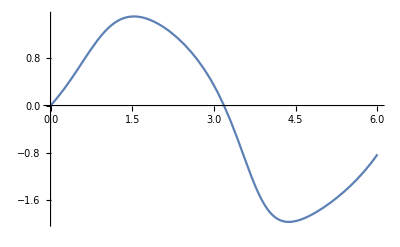

```mathematica
Plot[Evaluate[x[t]/.vdpsol[1,1,0,1,0,6]],{t,0,6}]
```

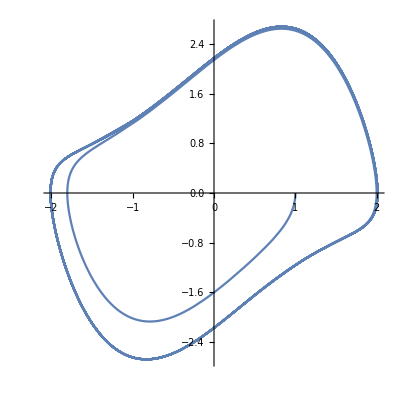

```mathematica
ParametricPlot[Evaluate[{x[t],v[t]}/.vdpsol[1,1,1,0,0,50]],{t,0,50},AspectRatio->1]
```